# DS Rate Study

## Setup: The Rate, the Delay and the Mass Distribution

## Star Formation Rate

It is logic to assume that BH merges are proportional to the Star Formation Rate (SFR). We use the Mandau function ψ that is in M_⊙Mpc^-3 yr^-1

```mathematica
ψ[z_]:=0.015*(1+z)^2.7/(1+((1+z)/2.9)^5.6)
```

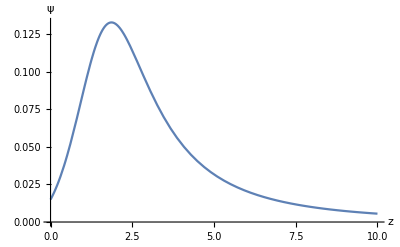

```mathematica
Plot[ψ[z],{z,0,10},AspectRatio->1/GoldenRatio,AxesLabel->{z,ψ}]
```

## Set the Cosmology

```mathematica
H0=70
```

70

```mathematica
tH=1000./H0
```

14.2857

```mathematica
Ωk=0;
```

```mathematica
Ωr=0
```

0

```mathematica
Ωm=0.3
```

0.3

```mathematica
Ωl=1-Ωm-Ωr
```

0.7

## Delay Function

Now that we have a SFR, we need to wait the natural life of the star in order to have some BBH. This is the ‘delay’. The delay can be modeled by an exponential decay but, for low probability, we can use 1/t as a good approximation. This t must be greater than the life of the star so t>tmin. In principle we have to take into account also the merging time for which we can not detect the  merging i.e. low and very low frequency but, since this lapse of time is negligible compared to the stellar life time,  we will ignore that .

```mathematica
EE[z_]:=(Ωm*(1+z)^3+Ωr*(1+z)^4+Ωk*(1+z)^2+Ωl)^(1/2)
```

```mathematica
cosmictime[z_]:=NIntegrate[tH/((1+x)*EE[x]),{x,z,+∞}]
```

```mathematica
zoft[t_]:=InverseFunction[cosmictime][t]
```

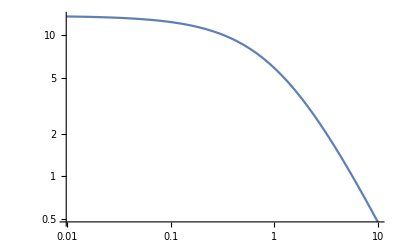

```mathematica
LogLogPlot[cosmictime[t],{t,0,10},PlotRange->All]
```

```mathematica
timefromnow[z_]:=NIntegrate[tH/((1+x)*EE[x]),{x,0,z}]
```

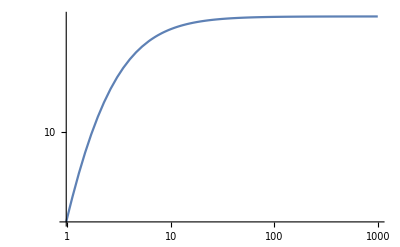

```mathematica
LogLogPlot[timefromnow[t],{t,0,1000},PlotRange->All]
```

```mathematica
zfromnow[t_]:=InverseFunction[timefromnow][t]
```

### Useful blocks

```mathematica
poft[t_]:=Piecewise[{{0,t<2},{1*2/t,t≥2}}]
```

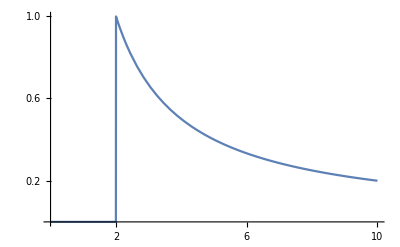

```mathematica
Plot[poft[t],{t,0,10},ScalingFunctions->{"Linear","Linear"},PlotRange->All]
```

```mathematica
tmin=2.
```

2.

```mathematica
deltime[z_]:=NIntegrate[tH/((1+x)*EE[x]),{x,z,zd},WorkingPrecision->MachinePrecision]
```

```mathematica
deltime[29]
```

-1.89531

```mathematica
zd=zoft[tmin]
```

3.20909

```mathematica
delay[z_]:=Piecewise[{{cosmictime[zd]/cosmictime[z],z<  zd},{1,z≥ zd}}]
```

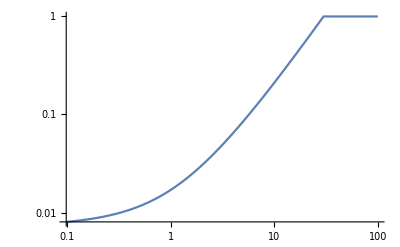

```mathematica
Plot[delay[t],{t,0,100},ScalingFunctions->{"Log","Log"},PlotRange->All]
```

```mathematica
tmin=2.
```

2.

```mathematica
zd=zoft[tmin]
```

3.20909

```mathematica
movingcosmictime[z_]:=(1+z)^-1*NIntegrate[tH/((1+x)*EE[x]),{x,z,+∞}]
```

```mathematica
newdelay[z_]:=Piecewise[{{movingcosmictime[zd]/movingcosmictime[z],z<  zd},{1,z≥ zd}}]
```

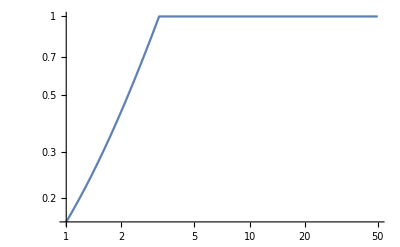

```mathematica
Plot[{(newdelay[t])},{t,1,50},ScalingFunctions->{"Log","Log"},PlotRange->All]
```

## GW Rate

Now we can compute the GW rate. We need a prescription for t(z) in order to have an integral over z.

```mathematica
(*RGW[z_]=μ*Integrate[-ψ[x]*1/teff*tH/((1+x)EE[x]),{x,z,+∞}] *) (*This is ok but is slow. A faster version below*)
```

```mathematica
(*RGW[from_]:=(int=μ*NIntegrate[-ψ[x]*1/teff*tH/((1+x)EE[x]),x];
Limit[int,x->+∞]-Limit[int,x->from])*)
```

### Evaluating the GW Rate & the Normalization (Other time def)

```mathematica
zd=zoft[10.]
```

0.329414

```mathematica
μ=25/NIntegrate[-ψ[x]*delay[0]*(tH/((1+x)*EE[x])),{x,0,∞},WorkingPrecision->MachinePrecision]
```

-42.6616

```mathematica
RGW[z_]:=μ*NIntegrate[-ψ[x]*delay[z]*(tH/((1+x)*EE[x])),{x,z,∞},WorkingPrecision->MachinePrecision]
```

```mathematica
RGW[0]
```

25.

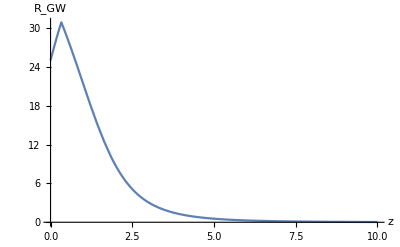

```mathematica
Plot[{RGW[z]},{z,0,10},AspectRatio->1/GoldenRatio,AxesLabel->{z,Subscript[R, GW]},PlotRange->All]
```

```mathematica
NewRateGW[z_]:=Piecewise[{{μ*NIntegrate[-ψ[x]*1/(cosmictime[z]-cosmictime[x])*(tH/((1+x)*EE[x])),{x,z,∞},WorkingPrecision->MachinePrecision],cosmictime[z]-cosmictime[x]>= tmin},{μ*NIntegrate[-ψ[x]*(tH/((1+x)*EE[x])),{x,z,∞},WorkingPrecision->MachinePrecision],cosmictime[z]-cosmictime[x]< tmin}}]
```

```mathematica
integrando[z_,x_]:=Piecewise[{{-ψ[x]*1/(cosmictime[z]-cosmictime[x])*(tH/((1+x)*EE[x])),cosmictime[z]-cosmictime[x]>= tmin},{-ψ[x]*(tH/((1+x)*EE[x])),cosmictime[z]-cosmictime[x]< tmin}}]
```

```mathematica
NIntegrate[integrando[1,x],{x,1,∞},WorkingPrecision->MachinePrecision]
```

NIntegrate::nlim: x = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand Piecewise[{{-(0.214286 (1+x)^1.7)/(√(0.69992+0.3 Power[«2»]+0.00008 Power[«2»]) (1+0.00257378 Power[«2»]) (5.8778-NIntegrate[«2»])), 5.8778-NIntegrate[Times[«2»],{«3»}]≥2.}, {-(0.214286 (1+x)^1.7)/(√(0.69992+0.3 Power[«2»]+0.00008 Power[«2»]) (1+0.00257378 Power[«2»])), 5.8778-NIntegrate[Times[«2»],{«3»}]<2.}, {0, True}}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,1.}}.

NIntegrate[integrando[1,x],{x,1,∞},WorkingPrecision→MachinePrecision]

```mathematica
tmin=0.1
```

0.1

```mathematica
NIntegrate[-ψ[x]*(Integrate[tH/((1+u)*EE[u]),{u,0,x}])^-1*(tH/((1+x)*EE[x])),{x,0,∞},WorkingPrecision->MachinePrecision]
```

NIntegrate::nlim: u = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
Integrate[tH/((1+u)*EE[u]),{u,0,x}]
```